#### code below generates Figure 2A

```mathematica
ClearAll["Global`*"]
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, μr,b,σ,ρ,ϕ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]},  
{s,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μr, b,σ,ρ,ϕ,n]=First@Evaluate[(σ (s[T]+ϕ r[T])/(1+ρ (s[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, μr_, b_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[vr[t], t]==γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr] -δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm] -δ vm[t]-β s[t]*vm[t],
D[r[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr]+β Exp[-τm μ]*s[t-τm]*vm[t-τm] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

solw[T_,tl_,τ_?NumericQ,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,sr0_,v0_]:=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vr0},{s,i,v,r},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
```

```mathematica
Clear[vr0,sr0]
v0=1;
list=Table[{τrx,τmx,v0=1; vr0=vcr[4,1,τrx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];sr0=sc[4,1,τrx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];vmx[4,1,τrx,τmx,10^-7,1,0.25,0.25,75]},{τrx,1,3.1,0.05},{τmx,1,3.1,0.05}];
```

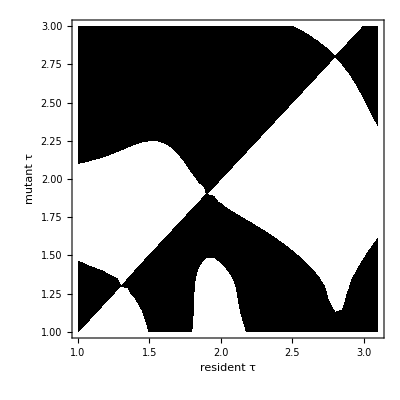

```mathematica
Flatten[list];
list=Partition[%,3];
noto=ListContourPlot[list,PlotLabel->Style["",16,Black],FrameLabel->{Style["resident τ",20,Black],Style["mutant τ",20,Black]},LabelStyle->Directive[Bold,FontFamily->"Palatino"],ContourStyle->None,ColorFunction->(If[#1>=1,Black,White]&),ColorFunctionScaling->False,FrameTicksStyle->15]
```

#### code below generates Figure 2B

transmission dynamics

```mathematica
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
solw[T_?NumericQ,tl_?NumericQ,τ_?NumericQ,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,s0_,v0_]:=
First@NDSolve[{D[s[t], t]==s0* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==v0},{s,i,v,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

```mathematica
essa=1.31;(*short latency ESS*)
v0=vcr[4,1,essa,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150]
s0=sc[4,1,essa,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150]
```

1.96035×10^7

978214.

```mathematica
essa=1.31;
v0=1.960349856417706*^7;
s0=978214.0888364211;
xb=Plot[{Evaluate[v[t]/.solw[4,1,essa,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,s0,v0]]},{t,0,4},Evaluated->True,PlotRange->{{0,4},{0,4*10^7}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01]}},AxesStyle->Opacity[0],Axes->False,Frame->True,FrameStyle->Thick];
essa=1.31;
v0=1.960349856417706*^7;
s0=978214.0888364211;
xc=Plot[{D[i[t]/.solw[4,1,essa,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,s0,v0],t]/.t->u/.t->u},{u,0,4},Evaluated->True,PlotRange->{{0,4},{0,800000}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01],Dashing[0.02]}},Frame->True,FrameStyle->Thick];
zz1=Labeled[Overlay[{xb,xc}],{Style["",FontFamily->"Helvetica",FontSize->22],Rotate[Style["
",FontFamily->"Helvetica",FontSize->22],180 Degree],Style["monocyclic attractor",FontFamily->"Helvetica",FontSize->28], Style["   parasite and host\n  infection dynamics",FontFamily->"Helvetica",FontSize->28]},{Bottom,Right,Top,Left},RotateLabel->True];
```

```mathematica
essb=2.8;(*long latency ESS*)
v0=vcr[4,1,essb,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150]
s0=sc[4,1,essb,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150]
```

3.30858×10^7

992752.

```mathematica
essb=2.8;
v0=3.3085791416635927*^7;
s0=992752.1385325898;
xb=Plot[{Evaluate[v[t]/.solw[4,1,essb,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,s0,v0]]},{t,0,4},Evaluated->True,PlotRange->{{0,4},{0,4*10^7}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01]}},AxesStyle->Opacity[0],Axes->False,Frame->True,FrameStyle->Thick];
essb=2.8;
v0=3.3085791416635927*^7;
s0=992752.1385325898;
xc=Plot[{D[i[t]/.solw[4,1,essb,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,s0,v0],t]/.t->u/.t->u},{u,0,4},Evaluated->True,PlotRange->{{0,4},{0,800000}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01],Dashing[0.02]}},Frame->True,FrameStyle->Thick];
zz2=Labeled[Overlay[{xb,xc}],{Style["time",FontFamily->"Helvetica",FontSize->22],Rotate[Style["
",FontFamily->"Helvetica",FontSize->22],180 Degree],Style["polycyclic attractor",FontFamily->"Helvetica",FontSize->28], Style["   parasite and host\n  infection dynamics",FontFamily->"Helvetica",FontSize->28]},{Bottom,Right,Top,Left},RotateLabel->True];
```

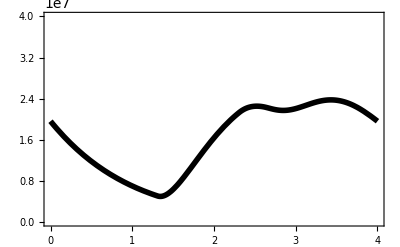
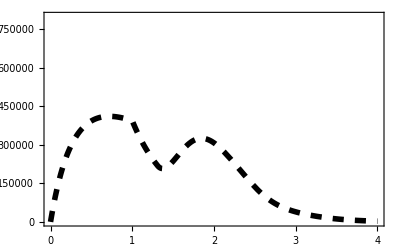
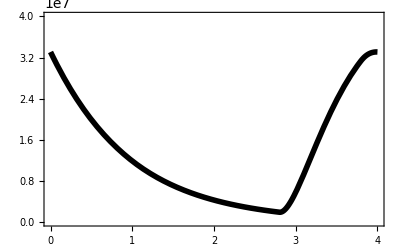
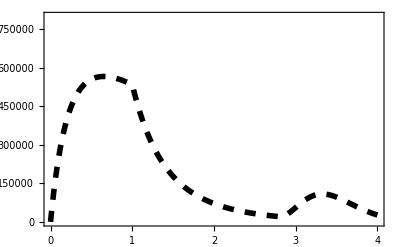
-Graphics--Graphics-
monocyclic attractor   parasite and host
  infection dynamics
-Graphics--Graphics-time
polycyclic attractor   parasite and host
  infection dynamics

```mathematica
n3=Style[Grid[{{zz1},{zz2}},Spacings->0],ImageSizeMultipliers->{1,1}]
```

#### code below generates Figure 3A-B

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, μr,b,σ,ρ,ϕ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]},  
{s,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μr, b,σ,ρ,ϕ,n]=First@Evaluate[(σ (s[T]+ϕ r[T])/(1+ρ (s[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, μr_, b_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[vr[t], t]==γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr] -δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm] -δ vm[t]-β s[t]*vm[t],
D[r[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr]+β Exp[-τm μ]*s[t-τm]*vm[t-τm] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

essfunc[listx_,ttx_,tlx_,tx_]:=(
alist=Select[listx,#[[2]]>0&];
If[Length@alist<2,(vr0=vcr[ttx,tlx,1,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];sr0=sc[ttx,tlx,1,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];
a=vmx[ttx,tlx,1,1+0.01,10^-7,1,0.25,0.25,75];If[a<1,ylist=Join[{{1,1}},alist]]), ylist=alist];
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;
zz=Flatten@yy;
If[Length[zz]>1,{minlist=Table[{τx,vcr[ttx,tlx,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];
sr0=sc[ttx,tlx,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];
ND[vmx[ttx,tlx,τrx,τrx,10^-7,1,0.25,0.25,75],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
repx={#1,#3}&@@@repp;
bb=Mean/@repx;yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
xm1=Transpose[{q,yy}];
If[Length[zz]>1,{inv=(vr0=vcr[ttx,tlx,zz[[1]],10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];
sr0=sc[ttx,tlx,zz[[1]],10^-7,1,0.25,0.25,75, 200,0.0001,0.5,100];
vmx[ttx,tlx,zz[[1]],zz[[2]],10^-7,1,0.25,0.25,75]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listtlx0=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

#### Figure 3A

```mathematica
listall=Table[listx=Table[{τx,  vr0=vcr[ttx,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];sr0=sc[ttx,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];
x=vmx[ttx,1,τx,τx+0.01,10^-7,1,0.25,0.25,75];
y=vmx[ttx,1,τx,τx-0.01,10^-7,1,0.25,0.25,75];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,ttx,1,ttx]},{τx,1,3.2,0.01}],{ttx,2.75,4.25,0.25}];
```

```mathematica
max=Select[listall,#[[3]]==1&];
rep=Select[listall,#[[3]]==2&];
min=Select[listall,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

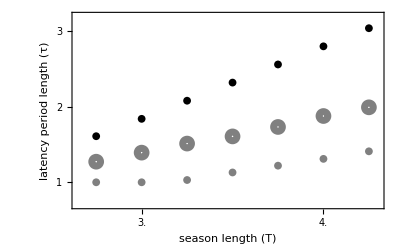

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,4.5,0.5],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{2.65,4.3},{0.7,3.2}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period length (τ)",16,FontFamily->"Helvetica"],None},{Style["season length (T)",16,FontFamily->"Helvetica"],Style["semelparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### Figure 3B

```mathematica
listall=Table[listx=Table[{τx,  vr0=vcr[ttx,1,τx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];sr0=sc[ttx,1,τx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];
x=vmx[ttx,1,τx,τx+0.01,10^-7,1,0.25,0.25,0.25,200,3];
y=vmx[ttx,1,τx,τx-0.01,10^-7,1,0.25,0.25,0.25,200,3];;
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,ttx,1,ttx]},{τx,1,3.2,0.01}],{ttx,2.75,4.25,0.25}];
```

```mathematica
max=Select[listall,#[[3]]==1&];
rep=Select[listall,#[[3]]==2&];
min=Select[listall,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

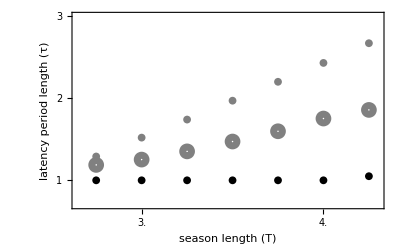

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,4.5,0.5],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{2.65,4.3},{0.7,3}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period length (τ)",16,FontFamily->"Helvetica"],None},{Style["season length (T)",16,FontFamily->"Helvetica"],Style["iteroparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### code below generates Figure 3C-D

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
ωx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ,μi, μr,b,σ,ρ,ϕ,γ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]},  
{s,i,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,n]=First@Evaluate[(σ (s[T]+ϕ i[T]+ ϕ r[T])/(1+ρ (s[T]+i[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_,μi_, μr_, b_,γ_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0 j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[ir[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr] -ir[t](μi +γ),
D[im[t], t]==β Exp[-τm μ]*s[t-τm]*vm[t-τm] -im[t](μi +γ),
D[r[t], t]==γ (ir[t]+im[t])-μr r[t],
D[vr[t], t]==ωx[τr,b] *ir[t]-δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==ωx[τm,b] *im[t]-δ vm[t]-β s[t]*vm[t],
s[t/;t≤0]==0,ir[t/;t≤0]==0,im[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

essfunc[listx_,ttx_,tlx_,tx_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_]:=(
alist=Select[listx,#[[2]]>0&];
If[Length@alist<2,(vr0=vcr[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];sr0=sc[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
a=vmx[ttx,tlx,1,1+0.01,β,δ,μ,μi,μr,b,γ];If[a<1,ylist=Join[{{1,1}},alist]]), ylist=alist];
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;
zz=Flatten@yy;
If[Length[zz]>1,{minlist=Table[{τx,vr0=vcr[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
sr0=sc[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
ND[vmx[ttx,tlx,τrx,τrx,β,δ,μ,μi,μr,b,γ],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
repx={#1,#3}&@@@repp;
bb=Mean/@repx;yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
xm1=Transpose[{q,yy}];
If[Length[zz]>1,{inv=(vr0=vcr[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
sr0=sc[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
vmx[ttx,tlx,zz[[1]],zz[[2]],β,δ,μ,μi,μr,b,γ]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listtlx0=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

#### Figure 3C

```mathematica
listall=Table[listx=Table[{τx, vr0=vcr[4,tlx,τx,10^-7,1,0.25,0.25,0.25,75, 200,0.0001,0.5,100];sr0=sc[4,tlx,τx,10^-7,1,0.25,0.25,0.25,75, 200,0.0001,0.5,100];
x=vmx[4,tlx,τx,τx+0.01,10^-7,1,0.25,0.25,0.25,75];
y=vmx[4,tlx,τx,τx-0.01,10^-7,1,0.25,0.25,0.25,75];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,tlx,tlx]},{τx,1,3.2,0.01}],{tlx,0.25,2.25,0.25}];
```

```mathematica
max=Select[listall,#[[3]]==1&];
rep=Select[listall,#[[3]]==2&];
min=Select[listall,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

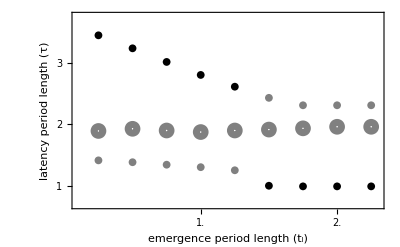

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,4.5,0.5],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.1,2.3},{0.7,3.75}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period length (τ)",16,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",16,FontFamily->"Helvetica"],Style["semelparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### Figure 3D

```mathematica
listall=Table[listx=Table[{τx, vr0=vcr[4,tlx,τx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];sr0=sc[4,tlx,τx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];
x=vmx[4,tlx,τx,τx+0.01,10^-7,1,0.25,0.25,0.25,200,3];
y=vmx[4,tlx,τx,τx-0.01,10^-7,1,0.25,0.25,0.25,200,3];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,tlx,tlx]},{τx,1,3.2,0.01}],{tlx,0.25,2.25,0.25}];
```

```mathematica
max=Select[listall,#[[3]]==1&];
rep=Select[listall,#[[3]]==2&];
min=Select[listall,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

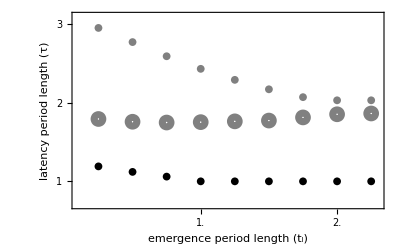

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,4.5,0.5],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.1,2.3},{0.7,3.1}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period length (τ)",16,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",16,FontFamily->"Helvetica"],Style["iteroparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### code below generates Figure 4A-B

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, μr,b,σ,ρ,ϕ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]},  
{s,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μr, b,σ,ρ,ϕ,n]=First@Evaluate[(σ (s[T]+ϕ r[T])/(1+ρ (s[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, μr_, b_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[vr[t], t]==γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr] -δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm] -δ vm[t]-β s[t]*vm[t],
D[r[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr]+β Exp[-τm μ]*s[t-τm]*vm[t-τm] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

essfunc[listx_,ttx_,tlx_,tx_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_]

essfunc[listx_,ttx_,tlx_,τx_,β_,δ_,μ_,μr_,b_,σ_,ρ_,ϕ_]:=(
alist=Select[listx,#[[2]]>0&];
If[Length@alist<2,(vr0=vcr[ttx,tlx,τx,β,δ,μ,μr, b,σ,ρ,ϕ,100];sr0=sc[ttx,tlx,τx,β,δ,μ,μr, b,σ,ρ,ϕ,100];
a=vmx[ttx,tlx,τx,τx+0.01,β,δ,μ,μr, b];If[a<1,ylist=Join[{{1,1}},alist]]), ylist=alist];
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;
zz=Flatten@yy;
If[Length[zz]>1,{minlist=Table[{τx,vcr[ttx,tlx,τx,β,δ,μ,μr, b,σ,ρ,ϕ,100];
sr0=sc[ttx,tlx,τx,β,δ,μ,μr, b,σ,ρ,ϕ,100];
ND[vmx[ttx,tlx,τx,τx,β,δ,μ,μr, b],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
repx={#1,#3}&@@@repp;
bb=Mean/@repx;yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
xm1=Transpose[{q,yy}];
If[Length[zz]>1,{inv=(vr0=vcr[ttx,tlx,zz[[1]],β,δ,μ,μr, b,σ,ρ,ϕ,100];
sr0=sc[ttx,tlx,zz[[1]],β,δ,μ,μr, b,σ,ρ,ϕ,100];
vmx[ttx,tlx,zz[[1]],zz[[2]],β,δ,μ,μr, b]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listtlx0=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

#### Figure 4A

```mathematica
list={0.25,0.55,1,2,3,4,5};
listall=Table[listx=Table[{τx, vr0=vcr[4,1,τx,10^-7,1,0.25,μrx,75, 200,0.0001,1,100];sr0=sc[4,1,τx,10^-7,1,0.25,μrx,75, 200,0.0001,1,100];
x=vmx[4,1,τx,τx+0.01,10^-7,1,0.25,μrx,75];
y=vmx[4,1,τx,τx-0.01,10^-7,1,0.25,μrx,75];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,1,μrx,10^-7,1,0.25,μrx,75, 200,0.0001,1]},{τx,1,3.2,0.01};],{μrx,list}];
```

```mathematica
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

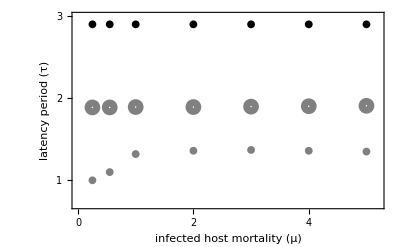

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,5,1],None}};
lptt=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0,5.2},{0.7,3}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period (τ)",16,FontFamily->"Helvetica"],None},{Style["infected host mortality (μ)",16,FontFamily->"Helvetica"],Style["semelparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### Figure 4B

```mathematica
listall=Table[listx=Table[{τx, vr0=vcr[4,1,τx,10^-7,1,0.25,μrx,μrx,200, 200,0.0001,0.5,3,300];sr0=sc[4,1,τx,10^-7,1,0.25,μrx,μrx,200, 200,0.0001,0.5,3,300];
x=vmx[4,1,τx,τx+0.01,10^-7,1,0.25,μrx,μrx,200,3];
y=vmx[4,1,τx,τx-0.01,10^-7,1,0.25,μrx,μrx,200,3];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,1,μrx,10^-7,1,0.25,μrx,μrx,100, 200,0.0001,0.5,3]},{τx,1,3.2,0.01};],{μrx,0.15,0.95,0.1}];
```

```mathematica
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

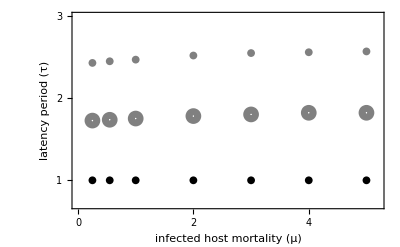

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,5,1],None}};
lptt=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0,5.2},{0.7,3}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period (τ)",16,FontFamily->"Helvetica"],None},{Style["infected host mortality (μ)",16,FontFamily->"Helvetica"],Style["iteroparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### code below generates Figure 4C-D

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
ωx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ,μi, μr,b,σ,ρ,ϕ,γ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]},  
{s,i,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,n]=First@Evaluate[(σ (s[T]+ϕ i[T]+ ϕ r[T])/(1+ρ (s[T]+i[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_,μi_, μr_, b_,γ_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0 j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[ir[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr] -ir[t](μi +γ),
D[im[t], t]==β Exp[-τm μ]*s[t-τm]*vm[t-τm] -im[t](μi +γ),
D[r[t], t]==γ (ir[t]+im[t])-μr r[t],
D[vr[t], t]==ωx[τr,b] *ir[t]-δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==ωx[τm,b] *im[t]-δ vm[t]-β s[t]*vm[t],
s[t/;t≤0]==0,ir[t/;t≤0]==0,im[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

essfunc[listx_,ttx_,tlx_,tx_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_]:=(
alist=Select[listx,#[[2]]>0&];
If[Length@alist<2,(vr0=vcr[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];sr0=sc[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
a=vmx[ttx,tlx,1,1+0.01,β,δ,μ,μi,μr,b,γ];If[a<1,ylist=Join[{{1,1}},alist]]), ylist=alist];
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;
zz=Flatten@yy;
If[Length[zz]>1,{minlist=Table[{τx,vr0=vcr[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
sr0=sc[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
ND[vmx[ttx,tlx,τrx,τrx,β,δ,μ,μi,μr,b,γ],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
repx={#1,#3}&@@@repp;
bb=Mean/@repx;yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
xm1=Transpose[{q,yy}];
If[Length[zz]>1,{inv=(vr0=vcr[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
sr0=sc[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
vmx[ttx,tlx,zz[[1]],zz[[2]],β,δ,μ,μi,μr,b,γ]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listtlx0=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

```mathematica
essfunc[listx_,ttx_,tlx_,tx_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_]:=(
alist=Select[listx,#[[2]]>0&];
If[Length@alist<2,(vr0=vcr[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];sr0=sc[ttx,tlx,1,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
a=vmx[ttx,tlx,1,1+0.01,β,δ,μ,μi,μr,b,γ];If[a<1,ylist=Join[{{1,1}},alist]]), ylist=alist];
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;
zz=Flatten@yy;
If[Length[zz]>1,{minlist=Table[{τx,vr0=vcr[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
sr0=sc[ttx,tlx,τx,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,300];
ND[vmx[ttx,tlx,τrx,τrx,β,δ,μ,μi,μr,b,γ],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
repx={#1,#3}&@@@repp;
bb=Mean/@repx;yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
xm1=Transpose[{q,yy}];
If[Length[zz]>1,{inv=(vr0=vcr[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
sr0=sc[ttx,tlx,zz[[1]],β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,100];
vmx[ttx,tlx,zz[[1]],zz[[2]],β,δ,μ,μi,μr,b,γ]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listtlx0=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

#### Figure 4C

```mathematica
listall=Table[listx=Table[{τx, vr0=vcr[4,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,ϕx,200];sr0=sc[4,1,τx,10^-7,1,0.25,0.25,75, 200,0.0001,ϕx,200];
x=vmx[4,1,τx,τx+0.01,10^-7,1,0.25,0.25,75];
y=vmx[4,1,τx,τx-0.01,10^-7,1,0.25,0.25,75];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,1,ϕx,10^-7,1,0.25,0.25,75, 200,0.0001,ϕx]},{τx,1,3.3,0.01};],{ϕx,0.15,0.95,0.1}];
```

```mathematica
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

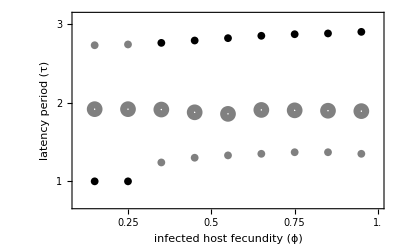

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,1,0.25],None}};
lptt=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.1,1},{0.7,3.1}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period (τ)",16,FontFamily->"Helvetica"],None},{Style["infected host fecundity (ϕ)",16,FontFamily->"Helvetica"],Style["semelparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### Figure 4D

```mathematica
listall=Table[listx=Table[{τx, vr0=vcr[4,1,τx,ϕx,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];sr0=sc[4,1,τx,ϕx,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,200];
x=vmx[4,1,τx,τx+0.01,ϕx,1,0.25,0.25,0.25,200,3];
y=vmx[4,1,τx,τx-0.01,ϕx,1,0.25,0.25,0.25,200,3];
If[x<1&&y<1,τxx=1,τxx=0];essfunc[listx,4,1,ϕx,10^-7,1,0.25,0.25,0.25,100, 200,0.0001,ϕx,3]},{τx,1,3.2,0.01};],{ϕx,0.15,0.95,0.1}];
```

```mathematica
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

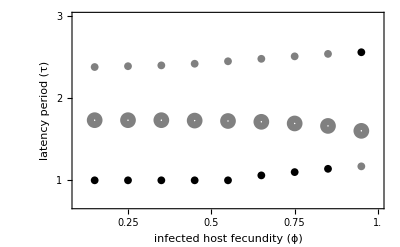

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,1,0.25],None}};
lptt=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.1,1},{0.7,3}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["latency period (τ)",16,FontFamily->"Helvetica"],None},{Style["infected host fecundity (ϕ)",16,FontFamily->"Helvetica"],Style["iteroparous transmission",16,FontFamily->"Helvetica"]}}]
```

#### code below generates Appendix Figure B1

below is the same as the code for Figure 2, except there is no trade-off between γ and τ

```mathematica
ClearAll["Global`*"]
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=200;
vcr[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, μr,b,σ,ρ,ϕ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,0]:=sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μr,b,σ,ρ,ϕ,n-1]},  
{s,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μr, b,σ,ρ,ϕ,n]=First@Evaluate[(σ (s[T]+ϕ r[T])/(1+ρ (s[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, μr_, b_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[vr[t], t]==γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr] -δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm] -δ vm[t]-β s[t]*vm[t],
D[r[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr]+β Exp[-τm μ]*s[t-τm]*vm[t-τm] -μr r[t],
s[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

solw[T_,tl_,τ_?NumericQ,β_,δ_,μ_,μr_, b_,σ_,ρ_,ϕ_,sr0_,v0_]:=NDSolve[{
D[s[t], t]==sr0* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
D[r[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -μr r[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vr0},{s,i,v,r},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
```

```mathematica
Clear[vr0,sr0]
v0=1;
list2=Table[{τrx,τmx,v0=1; vr0=vcr[4,1,τrx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];sr0=sc[4,1,τrx,10^-7,1,0.25,0.25,75, 200,0.0001,0.5,150];vmx[4,1,τrx,τmx,10^-7,1,0.25,0.25,75]},{τrx,1,3.1,0.1},{τmx,1,3.1,0.1}];
```

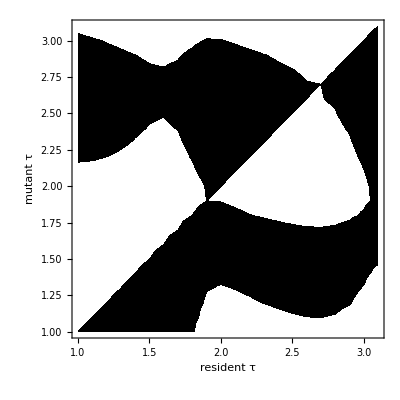

```mathematica
Flatten[list2];
list=Partition[%,3];
noto=ListContourPlot[list,PlotLabel->Style["",16,Black],FrameLabel->{Style["resident τ",20,Black],Style["mutant τ",20,Black]},LabelStyle->Directive[Bold,FontFamily->"Palatino"],ContourStyle->None,ColorFunction->(If[#1>=1,Black,White]&),ColorFunctionScaling->False,FrameTicksStyle->15]
```

#### code below generates Appendix Figure B2

```mathematica
ClearAll["Global`*"]
```

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
ωx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ,μi, μr,b,σ,ρ,ϕ,γ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]},  
{s,i,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,n]=First@Evaluate[(σ (s[T]+ϕ i[T]+ ϕ r[T])/(1+ρ (s[T]+i[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_,μi_, μr_, b_,γ_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0 j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[ir[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr] -ir[t](μi +γ),
D[im[t], t]==β Exp[-τm μ]*s[t-τm]*vm[t-τm] -im[t](μi +γ),
D[r[t], t]==γ (ir[t]+im[t])-μr r[t],
D[vr[t], t]==ωx[τr,b] *ir[t]-δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==ωx[τm,b] *im[t]-δ vm[t]-β s[t]*vm[t],
s[t/;t≤0]==0,ir[t/;t≤0]==0,im[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]
```

```mathematica
Clear[vr0,sr0]
v0=1;
list=Table[{τrx,τmx,v0=1; vr0=vcr[4,1,τrx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,150];sr0=sc[4,1,τrx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,150];vmx[4,1,τrx,τmx,10^-7,1,0.25,0.25,0.25,200,3]},{τrx,1,3.1,0.05},{τmx,1,3.1,0.05}];
```

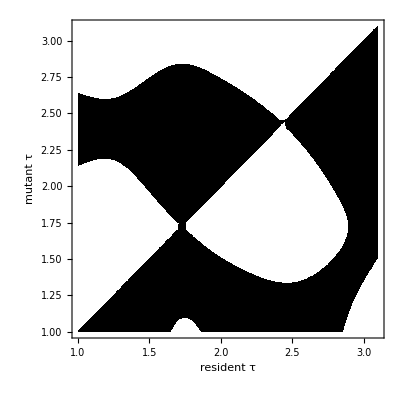

```mathematica
Flatten[list];
list=Partition[%,3];
noto=ListContourPlot[list,PlotLabel->Style["",16,Black],FrameLabel->{Style["resident τ",20,Black],Style["mutant τ",20,Black]},LabelStyle->Directive[Bold,FontFamily->"Palatino"],ContourStyle->None,ColorFunction->(If[#1>=1,Black,White]&),ColorFunctionScaling->False,FrameTicksStyle->15]
```

below is the same as above, except there is no trade-off between γ and τ

```mathematica
ClearAll["Global`*"]
```

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=1;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
ωx[τx_,b_]:=400;
vcr[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ,μi, μr,b,σ,ρ,ϕ,γ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,0]:=sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_,μi_,μr_, b_,σ_,ρ_,ϕ_,γ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]* j[t,tl]-μ s[t]-β s[t]*v[t],
D[i[t], t]==β Exp[-τ μ]*s[t-τ]*v[t-τ] -i[t](μi +γ),
D[r[t], t]==γ i[t]-μr r[t],
D[v[t], t]==ωx[τ,b] *i[t]-δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,i[t/;t≤0]==0,r[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,μi,μr,b,σ,ρ,ϕ,γ,n-1]},  
{s,i,r},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ,μi,μr, b,σ,ρ,ϕ,γ,n]=First@Evaluate[(σ (s[T]+ϕ i[T]+ ϕ r[T])/(1+ρ (s[T]+i[T]+r[T])))/.sol])
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_,μi_, μr_, b_,γ_]:=
(sol1=NDSolve[{
D[s[t], t]==sr0 j[t,tl]-μ s[t]-β s[t](vr[t]+vm[t]),
D[ir[t], t]==β Exp[-τr μ]*s[t-τr]*vr[t-τr] -ir[t](μi +γ),
D[im[t], t]==β Exp[-τm μ]*s[t-τm]*vm[t-τm] -im[t](μi +γ),
D[r[t], t]==γ (ir[t]+im[t])-μr r[t],
D[vr[t], t]==ωx[τr,b] *ir[t]-δ vr[t]-β s[t]*vr[t],
D[vm[t], t]==ωx[τm,b] *im[t]-δ vm[t]-β s[t]*vm[t],
s[t/;t≤0]==0,ir[t/;t≤0]==0,im[t/;t≤0]==0,r[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]
```

```mathematica
Clear[vr0,sr0]
v0=1;
list=Table[{τrx,τmx,v0=1; vr0=vcr[4,1,τrx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,150];sr0=sc[4,1,τrx,10^-7,1,0.25,0.25,0.25,200, 200,0.0001,0.5,3,150];vmx[4,1,τrx,τmx,10^-7,1,0.25,0.25,0.25,200,3]},{τrx,1,3.1,0.05},{τmx,1,3.1,0.05}];
```

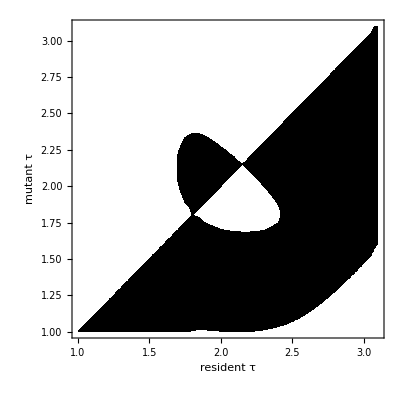

```mathematica
Flatten[list];
list=Partition[%,3];
noto=ListContourPlot[list,PlotLabel->Style["",16,Black],FrameLabel->{Style["resident τ",20,Black],Style["mutant τ",20,Black]},LabelStyle->Directive[Bold,FontFamily->"Palatino"],ContourStyle->None,ColorFunction->(If[#1>=1,Black,White]&),ColorFunctionScaling->False,FrameTicksStyle->15]
```